### Partial derivatives of Doppler equation Carl Tape and Bella Seppi August 29, 2025

```mathematica
Clear[t,Ft,FfactorA,Ffactor]
```

```mathematica
Clear[v0,tp0,l,f0,c,tp]
```

### Main equations for the Doppler frequency (Meng and Ben-Zion, 2018, Eq. 3b). Note that tp is the dependent variable and should be thought of a time in the spectrogram. Note that FfactorA < 0, Ffactor < 1, and Ft > f0.

```mathematica
t[v0_,tp0_,l_,c_,tp_]:=((tp-tp0)-Sqrt[(tp-tp0)^2-(1-v0^2/c^2)((tp-tp0)^2-l^2/c^2)])/(1-v0^2/c^2);
FfactorA[v0_,tp0_,l_,c_,tp_]:=v0/c(v0 t[v0,tp0,l,c,tp])/Sqrt[l^2+(v0 t[v0,tp0,l,c,tp])^2]
Ffactor[v0_,tp0_,l_,c_,tp_]:=1+FfactorA[v0,tp0,l,c,tp];
Ft[v0_,tp0_,l_,f0_,c_,tp_]:=f0/Ffactor[v0,tp0,l,c,tp];
```

### Find the limiting values for Fapproach (higher frequency; flying toward) and Frecede (lower frequency; flying away). (This takes a minute.)

```mathematica
Limit[Ft[v0,tp0,l,f0,c,tp],tp->-Infinity]
Limit[Ft[v0,tp0,l,f0,c,tp],tp->Infinity]
```

f0/(1-((c^2-v0^2) √((c^4 v0^2 (1+√(v0^2/c^2))^2)/((c^2-v0^2)^2)))/(c^3 (1+√(v0^2/c^2))))

f0/(1+((-c^2+v0^2) √((c^4 v0^2 (-1+√(v0^2/c^2))^2)/((c^2-v0^2)^2)))/(c^3 (-1+√(v0^2/c^2))))

```mathematica
Fapproach[v0_,f0_,c_]:=f0/(1-((c^2-v0^2) √((c^4 v0^2 (1+√(v0^2/c^2))^2)/((c^2-v0^2)^2)))/(c^3 (1+√(v0^2/c^2))))
```

```mathematica
Frecede[v0_,f0_,c_]:=f0/(1+((-c^2+v0^2) √((c^4 v0^2 (-1+√(v0^2/c^2))^2)/((c^2-v0^2)^2)))/(c^3 (-1+√(v0^2/c^2))))
```

```mathematica
Fmean[v0_,f0_,c_]:=(Fapproach[v0,f0,c]+Frecede[v0,f0,c])/2
```

```mathematica
Frange[v0_,f0_,c_]:=Fapproach[v0,f0,c]-Frecede[v0,f0,c]
```

```mathematica
FullSimplify[Frange[v0,f0,c]]
```

f0/(1+((-c^2+v0^2) √(1/(1/c^2+(1-2 √(v0^2/c^2))/v0^2)))/(c^3 (1+√(v0^2/c^2))))-f0/(1+((-c^2+v0^2) √(1/(1/c^2+(1+2 √(v0^2/c^2))/v0^2)))/(c^3 (-1+√(v0^2/c^2))))

### Let ε = v0/c. Re-write as a series in ε, then consider approximations.

```mathematica
expr=Frange[v0,f0,c];
exprSub=expr/. v0->ε c;
FullSimplify[exprSub]
Series[exprSub,{ε,0,4}]//Normal//FullSimplify
Series[exprSub,{ε,0,2}]//Normal//FullSimplify
```

f0 ((c-c √(ε^2))/(c (-1+√(ε^2))+(-1+ε^2) √((c^2 (ε^2+ε^4-2 (ε^2)^(3/2)))/((-1+ε^2)^2)))+(c (1+√(ε^2)))/(c (1+√(ε^2))+(-1+ε^2) √((c^2 (ε^2+ε^4+2 (ε^2)^(3/2)))/((-1+ε^2)^2))))

(2 f0 √(c^2 ε^2) (1+ε^2))/c

(2 f0 √(c^2 ε^2))/c

```mathematica
Frangeapprox2[v0_,f0_,c_]:=2 f0 (v0/c)
```

```mathematica
Frangeapprox4[v0_,f0_,c_]:=Frangeapprox2[v0,f0,c](1+(v0/c)^2)
```

### This function will reduce some of the later expressions:

```mathematica
G[v0_,tp0_,l_,c_,tp_]:=√((-l^2 v0^2+c^2 (l^2+(tp-tp0)^2 v0^2))/c^4)
```

### Here’s full simplification of Ft[ ], though I don’t think it helps:

```mathematica
FullSimplify[Ft[v0,tp0,l,f0,c,tp]]
```

f0/(1-(c v0^2 (-tp+tp0+√((-l^2 v0^2+c^2 (l^2+(tp-tp0)^2 v0^2))/c^4)))/((c^2-v0^2) √(l^2+(c^4 v0^2 (-tp+tp0+√((-l^2 v0^2+c^2 (l^2+(tp-tp0)^2 v0^2))/c^4))^2)/((c^2-v0^2)^2))))

### Here’s the expression in terms of G[ ]

```mathematica
f0/(1-(c v0^2 (-tp+tp0+G[v0,tp0,l,c,tp]))/((c^2-v0^2) √(l^2+(c^4 v0^2 (-tp+tp0+G[v0,tp0,l,c,tp])^2)/((c^2-v0^2)^2))))
```

f0/(1-(c v0^2 (-tp+tp0+√((-l^2 v0^2+c^2 (l^2+(tp-tp0)^2 v0^2))/c^4)))/((c^2-v0^2) √(l^2+(c^4 v0^2 (-tp+tp0+√((-l^2 v0^2+c^2 (l^2+(tp-tp0)^2 v0^2))/c^4))^2)/((c^2-v0^2)^2))))

### Partial derivative expressions, fully simplified. These expressions take a few minutes to derive. They can be commented out, since we define explicit expressions.

### Speed of source, v0

```mathematica
(* FullSimplify[D[Ft[v0,tp0,l,f0,c,tp],v0]] *)
```

```mathematica
partialv[v0_,tp0_,l_,f0_,c_,tp_]:=-((f0 v0 (-2 l^4 v0^4+l^2 (tp-tp0)^2 v0^6+c^6 (tp-tp0) (2 l^2+(tp-tp0)^2 v0^2) G[v0,tp0,l,c,tp]+c^2 (4 l^4 v0^2-(tp-tp0)^4 v0^6+l^2 (tp-tp0) v0^4 (5 tp-5 tp0-3 G[v0,tp0,l,c,tp]))-c^4 (2 l^4-3 (tp-tp0)^3 v0^4 (-tp+tp0+G[v0,tp0,l,c,tp])-l^2 (tp-tp0) v0^2 (-6 tp+6 tp0+G[v0,tp0,l,c,tp]))))/(c (c-v0) (c+v0) G[v0,tp0,l,c,tp] √(l^2+(c^4 v0^2 (-tp+tp0+G[v0,tp0,l,c,tp])^2)/((c^2-v0^2)^2)) (c (-tp+tp0) v0^2+c v0^2 G[v0,tp0,l,c,tp]-c^2 √(l^2+(c^4 v0^2 (-tp+tp0+G[v0,tp0,l,c,tp])^2)/((c^2-v0^2)^2))+v0^2 √(l^2+(c^4 v0^2 (-tp+tp0+G[v0,tp0,l,c,tp])^2)/((c^2-v0^2)^2)))^2))
```

### Unshifted frequency, f0 (note: it does not depend on f0)

```mathematica
(* FullSimplify[D[Ft[v0,tp0,l,f0,c,tp],f0]] *)
```

```mathematica
partialf[v0_,tp0_,l_,f0_,c_,tp_]:=1/(1-(c v0^2 (-tp+tp0+G[v0,tp0,l,c,tp]))/((c^2-v0^2) √(l^2+(c^4 v0^2 (-tp+tp0+G[v0,tp0,l,c,tp])^2)/((c^2-v0^2)^2))))
```

### Arrival time, tp0

```mathematica
(* FullSimplify[D[Ft[v0,tp0,l,f0,c,tp],tp0]] *)
```

```mathematica
partialtp[v0_,tp0_,l_,f0_,c_,tp_]:=(f0 l^2 (c-v0) v0^2 (c+v0) ((-tp+tp0) v0^2+c^2 G[v0,tp0,l,c,tp]))/(c G[v0,tp0,l,c,tp] √(l^2+(c^4 v0^2 (-tp+tp0+G[v0,tp0,l,c,tp])^2)/((c^2-v0^2)^2)) (c (-tp+tp0) v0^2+c v0^2 G[v0,tp0,l,c,tp]-c^2 √(l^2+(c^4 v0^2 (-tp+tp0+ G[v0,tp0,l,c,tp])^2)/((c^2-v0^2)^2))+v0^2 √(l^2+(c^4 v0^2 (-tp+tp0+G[v0,tp0,l,c,tp])^2)/((c^2-v0^2)^2)))^2)
```

### Distance to object, l

```mathematica
(* FullSimplify[D[Ft[v0,tp0,l,f0,c,tp],l]] *)
```

```mathematica
partiall[v0_,tp0_,l_,f0_,c_,tp_]:=(f0 l (tp-tp0) (c-v0) v0^2 (c+v0) ((-tp+tp0) v0^2+c^2 G[v0,tp0,l,c,tp]))/(c G[v0,tp0,l,c,tp]  √(l^2+(c^4 v0^2 (-tp+tp0+G[v0,tp0,l,c,tp])^2)/((c^2-v0^2)^2)) (c (-tp+tp0) v0^2+c v0^2 G[v0,tp0,l,c,tp]-c^2 √(l^2+(c^4 v0^2 (-tp+tp0+G[v0,tp0,l,c,tp])^2)/((c^2-v0^2)^2))+v0^2 √(l^2+(c^4 v0^2 (-tp+tp0+G[v0,tp0,l,c,tp])^2)/((c^2-v0^2)^2)))^2)
```

### Acoustic wavespeed, c

```mathematica
(* FullSimplify[D[Ft[v0,tp0,l,f0,c,tp],c]] *)
```

```mathematica
partialc[v0_,tp0_,l_,f0_,c_,tp_]:=(f0 v0^2 (-2 l^4 v0^4+2 l^2 (tp-tp0)^2 v0^6+c^6 (tp-tp0) (l^2+(tp-tp0)^2 v0^2) G[v0,tp0,l,c,tp]+c^2 (4 l^4 v0^2-(tp-tp0)^4 v0^6+l^2 (tp-tp0) v0^4 (3 tp-3 tp0-4 G[v0,tp0,l,c,tp]))-c^4 (l^2+(tp-tp0)^2 v0^2) (2 l^2-3 (tp-tp0) v0^2 (-tp+tp0+G[v0,tp0,l,c,tp] ))))/(c^2 (c-v0) (c+v0) G[v0,tp0,l,c,tp] √(l^2+(c^4 v0^2 (-tp+tp0+G[v0,tp0,l,c,tp])^2)/((c^2-v0^2)^2)) (c (-tp+tp0) v0^2+c v0^2 G[v0,tp0,l,c,tp]-c^2 √(l^2+(c^4 v0^2 (-tp+tp0+G[v0,tp0,l,c,tp])^2)/((c^2-v0^2)^2))+v0^2 √(l^2+(c^4 v0^2 (-tp+tp0+G[v0,tp0,l,c,tp])^2)/((c^2-v0^2)^2)))^2)
```

### First derivative w.r.t. time (tp)

```mathematica
FullSimplify[D[Ft[v0,tp0,l,f0,c,tp],{tp,1}]]
```

-((f0 l^2 (c-v0) v0^2 (c+v0) ((-tp+tp0) v0^2+c^2 √((-l^2 v0^2+c^2 (l^2+(tp-tp0)^2 v0^2))/c^4)))/(c √((-l^2 v0^2+c^2 (l^2+(tp-tp0)^2 v0^2))/c^4) √(l^2+(c^4 v0^2 (-tp+tp0+√((-l^2 v0^2+c^2 (l^2+(tp-tp0)^2 v0^2))/c^4))^2)/((c^2-v0^2)^2)) (c (-tp+tp0) v0^2+c v0^2 √((-l^2 v0^2+c^2 (l^2+(tp-tp0)^2 v0^2))/c^4)-c^2 √(l^2+(c^4 v0^2 (-tp+tp0+√((-l^2 v0^2+c^2 (l^2+(tp-tp0)^2 v0^2))/c^4))^2)/((c^2-v0^2)^2))+v0^2 √(l^2+(c^4 v0^2 (-tp+tp0+√((-l^2 v0^2+c^2 (l^2+(tp-tp0)^2 v0^2))/c^4))^2)/((c^2-v0^2)^2)))^2))

```mathematica
D1F[v0_,tp0_,l_,f0_,c_,tp_]:=-((f0 l^2 (c-v0) v0^2 (c+v0) ((-tp+tp0) v0^2+c^2 G[v0,tp0,l,c,tp]))/(c G[v0,tp0,l,c,tp] √(l^2+(c^4 v0^2 (-tp+tp0+G[v0,tp0,l,c,tp])^2)/((c^2-v0^2)^2)) (c (-tp+tp0) v0^2+c v0^2 G[v0,tp0,l,c,tp]-c^2 √(l^2+(c^4 v0^2 (-tp+tp0+G[v0,tp0,l,c,tp])^2)/((c^2-v0^2)^2))+v0^2 √(l^2+(c^4 v0^2 (-tp+tp0+G[v0,tp0,l,c,tp])^2)/((c^2-v0^2)^2)))^2 ))
```

### Second derivative w.r.t. time (tp)

```mathematica
(*FullSimplify[D[Ft[v0,tp0,l,f0,c,tp],{tp,2}]]*)  (* this calculation did not finish in >12 hours *)
```

```mathematica
(* Simplify[D[Ft[v0,tp0,l,f0,c,tp],{tp,2}]] *)
```

```mathematica
D2f[v0_,tp0_,l_,f0_,c_,tp_]:=(f0 (2 c l^4 v0^4 (c^2-v0^2)^4 G[v0,tp0,l,c,tp] (-tp v0^2+tp0 v0^2+c^2 G[v0,tp0,l,c,tp])^2-1/c^2 v0^4 (-3 c^10 v0^2 G[v0,tp0,l,c,tp] (-tp+tp0+G[v0,tp0,l,c,tp])^3 (-tp v0^2+tp0 v0^2+c^2 G[v0,tp0,l,c,tp])^2-c^4 l^2 v0^2 (-c^2+v0^2) (-tp+tp0+G[v0,tp0,l,c,tp])^2 (l^2 (c^2-v0^2)^2+c^4 v0^2 (-tp+tp0+G[v0,tp0,l,c,tp])^2)-3 c^6 G[v0,tp0,l,c,tp] (tp-tp0-G[v0,tp0,l,c,tp]) ((tp-tp0) v0^2-c^2 G[v0,tp0,l,c,tp])^2 (l^2 (c^2-v0^2)^2+c^4 v0^2 (-tp+tp0+G[v0,tp0,l,c,tp])^2)+l^2 (-c^2+v0^2) (l^2 (c^2-v0^2)^2+c^4 v0^2 (-tp+tp0+G[v0,tp0,l,c,tp])^2)^2) (-c v0^2 (-tp+tp0+G[v0,tp0,l,c,tp])+(c^2-v0^2) √(l^2+(c^4 v0^2 (-tp+tp0+G[v0,tp0,l,c,tp])^2)/((c^2-v0^2)^2)))))/(c^3 (c^2-v0^2)^6 (G[v0,tp0,l,c,tp])^3 (l^2+(c^4 v0^2 (-tp+tp0+G[v0,tp0,l,c,tp])^2)/((c^2-v0^2)^2))^3 (1-(c v0^2 (-tp+tp0+G[v0,tp0,l,c,tp]))/((c^2-v0^2) √(l^2+(c^4 v0^2 (-tp+tp0+G[v0,tp0,l,c,tp])^2)/((c^2-v0^2)^2))))^3)
```

```mathematica
(* Simplify[D[Ft[v0,tp0,l,f0,c,tp],{tp,3}]] *)
```

```mathematica
D3f[v0_,tp0_,l_,f0_,c_,tp_]:=-((3 f0 (2 l^6 v0^6 (c^2-v0^2)^6 (-l^2 v0^2+c^2 (l^2+(tp-tp0)^2 v0^2)) (-tp v0^2+tp0 v0^2+c^2 G[v0,tp0,l,c,tp])^3+2 c l^2 v0^6 (c^2-v0^2)^2 G[v0,tp0,l,c,tp] ((tp-tp0) v0^2-c^2 G[v0,tp0,l,c,tp]) (-3 c^10 v0^2 G[v0,tp0,l,c,tp] (-tp+tp0+G[v0,tp0,l,c,tp])^3 (-tp v0^2+tp0 v0^2+c^2 G[v0,tp0,l,c,tp])^2-c^4 l^2 v0^2 (-c^2+v0^2) (-tp+tp0+G[v0,tp0,l,c,tp])^2 (l^2 (c^2-v0^2)^2+c^4 v0^2 (-tp+tp0+G[v0,tp0,l,c,tp])^2)-3 c^6 G[v0,tp0,l,c,tp] (tp-tp0-G[v0,tp0,l,c,tp]) ((tp-tp0) v0^2-c^2 G[v0,tp0,l,c,tp])^2 (l^2 (c^2-v0^2)^2+c^4 v0^2 (-tp+tp0+G[v0,tp0,l,c,tp])^2)+l^2 (-c^2+v0^2) (l^2 (c^2-v0^2)^2+c^4 v0^2 (-tp+tp0+G[v0,tp0,l,c,tp])^2)^2) (-c v0^2 (-tp+tp0+G[v0,tp0,l,c,tp])+(c^2-v0^2) √(l^2+(c^4 v0^2 (-tp+tp0+G[v0,tp0,l,c,tp])^2)/((c^2-v0^2)^2)))+(5 c^10 v0^8 (-l^2 v0^2+c^2 (l^2+(tp-tp0)^2 v0^2)) (-tp+tp0+G[v0,tp0,l,c,tp])^4 ((tp-tp0) v0^2-c^2 G[v0,tp0,l,c,tp])^3+3 c^8 l^2 v0^8 (-c^2+v0^2) G[v0,tp0,l,c,tp] (-tp+tp0+G[v0,tp0,l,c,tp])^3 ((tp-tp0) v0^2-c^2 G[v0,tp0,l,c,tp]) (l^2 (c^2-v0^2)^2+c^4 v0^2 (-tp+tp0+G[v0,tp0,l,c,tp])^2)-6 c^6 v0^6 (-l^2 v0^2+c^2 (l^2+(tp-tp0)^2 v0^2)) (-tp+tp0+G[v0,tp0,l,c,tp])^2 ((tp-tp0) v0^2-c^2 G[v0,tp0,l,c,tp])^3 (l^2 (c^2-v0^2)^2+c^4 v0^2 (-tp+tp0+G[v0,tp0,l,c,tp])^2)+c^4 l^2 (tp-tp0) v0^8 (-c^2+v0^2) (-tp+tp0+G[v0,tp0,l,c,tp])^2 (l^2 (c^2-v0^2)^2+c^4 v0^2 (-tp+tp0+G[v0,tp0,l,c,tp])^2)^2+3 c^4 l^2 v0^6 (-c^2+v0^2) G[v0,tp0,l,c,tp] (tp-tp0-G[v0,tp0,l,c,tp]) ((tp-tp0) v0^2-c^2 G[v0,tp0,l,c,tp]) (l^2 (c^2-v0^2)^2+c^4 v0^2 (-tp+tp0+G[v0,tp0,l,c,tp])^2)^2+c^2 v0^4 (-l^2 v0^2+c^2 (l^2+(tp-tp0)^2 v0^2)) ((tp-tp0) v0^2-c^2 G[v0,tp0,l,c,tp])^3 (l^2 (c^2-v0^2)^2+c^4 v0^2 (-tp+tp0+G[v0,tp0,l,c,tp])^2)^2-l^2 (tp-tp0) v0^6 (-c^2+v0^2) (l^2 (c^2-v0^2)^2+c^4 v0^2 (-tp+tp0+G[v0,tp0,l,c,tp])^2)^3) (c v0^2 (-tp+tp0+G[v0,tp0,l,c,tp])+(-c^2+v0^2) √(l^2+(c^4 v0^2 (-tp+tp0+G[v0,tp0,l,c,tp])^2)/((c^2-v0^2)^2)))^2))/(c^7 (c^2-v0^2)^9 G[v0,tp0,l,c,tp]^5 (l^2+(c^4 v0^2 (-tp+tp0+G[v0,tp0,l,c,tp])^2)/((c^2-v0^2)^2))^(9/2) (-1+(c v0^2 (-tp+tp0+G[v0,tp0,l,c,tp]))/((c^2-v0^2) √(l^2+(c^4 v0^2 (-tp+tp0+G[v0,tp0,l,c,tp])^2)/((c^2-v0^2)^2))))^4))
```

### Trying to define a series, to consider dropping higher-order terms.

```mathematica
expr=D2f[v0,tp0,l,f0,c,tp];
exprSub=expr/. v0->ε c;
FullSimplify[Series[exprSub,{ε,0,6}]]
```

(c^2 f0 (2 l^4+c (l^2)^(3/2) (-2 √(l^2/c^2)+3 tp-3 tp0)) ε^4)/l^6+1/(2 l^4)3 c^2 f0 (-4 l^2+4 c^2 (tp-tp0) (3 √(l^2/c^2)-2 tp+2 tp0)+(c^3 (tp-tp0)^2 (8 √(l^2/c^2)-5 tp+5 tp0))/(√(l^2))+c √(l^2) (4 √(l^2/c^2)-7 tp+7 tp0)) ε^6+O[ε]^7

## What is the difference between the picked F(tp0) and f0?

```mathematica
Ft[v0,tp0,l,f0,c,tp]
```

f0/(1+(v0^2 (tp-tp0-√((tp-tp0)^2-(-l^2/c^2+(tp-tp0)^2) (1-v0^2/c^2))))/(c (1-v0^2/c^2) √(l^2+(v0^2 (tp-tp0-√((tp-tp0)^2-(-l^2/c^2+(tp-tp0)^2) (1-v0^2/c^2)))^2)/((1-v0^2/c^2)^2))))

```mathematica
Ft[v0,tp0,l,f0,c,tp0]
```

f0/(1-(v0^2 √((l^2 (1-v0^2/c^2))/c^2))/(c (1-v0^2/c^2) √(l^2+(l^2 v0^2)/(c^2 (1-v0^2/c^2)))))

```mathematica
FullSimplify[Ft[v0,tp0,l,f0,c,tp0]-f0]
```

f0 (-1+1/(1-(v0^2 √((l^2 (c-v0) (c+v0))/c^4) √((c^2 l^2)/(c^2-v0^2)))/(c l^2)))

### This is just a formula in terms of f0, v0, and c:

```mathematica
Simplify[1/(1-v0^2/c^2)-1]
```

v0^2/(c^2-v0^2)

```mathematica
Fshiftfactor[v0_,c_]:= v0^2/(c^2-v0^2)
```

```mathematica
Fshift[f0_,v0_,c_]:=f0 Fshiftfactor[v0,c]
```

### Example calculation:

```mathematica
vx=121.6;
fx=121.0;
cx=311.1;
N[Ft[vx,tpx,lx,fx,cx,tpx]-fx]
N[Fshift[fx,vx,cx]]
N[Fshiftfactor[vx,cx]]
```

21.8201

21.8201

0.180331

## Preliminaries

### Find the slope of the doppler at the center. That means finding the root for the second derivative.

```mathematica
(* Solve[D[Ft[v0,tp0,l,f0,c,tp],{tp,2}]==0,tp] *)  (* not sure if this will run *)
```

### Find the inflection points by setting the third derivative to zero and solving.

```mathematica
(* Solve[D[Ft[v0,tp0,l,f0,c,tp],{tp,3}]==0,tp] *)  (* this probably does not finish *)
```

### Example plot

```mathematica
c = 343;
v0 = 50;
tp0= 115;
l = 1000;
f0 = 100;
```

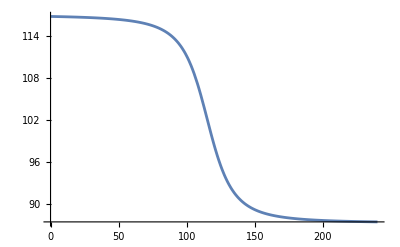

```mathematica
Plot[Ft[v0,tp0,l,f0,c,tp],{tp,0,240}]
```

```mathematica
f0
```

100

```mathematica
N[Ft[v0,tp0,l,f0,c,tp0]]
N[FfactorA[v0,tp0,l,c,tp0]]
N[Ffactor[v0,tp0,l,c,tp0]]
```

102.171

-0.0212496

0.97875

### list the approximations for the fmax (fminus) and fmin (fplus) frequencies

```mathematica
N[Fapproach[v0,f0,c]]
N[Frecede[v0,f0,c]]
N[Fmean[v0,f0,c]]
N[Frange[v0,f0,c]]
N[Frangeapprox4[v0,f0,c]]
N[Frangeapprox2[v0,f0,c]]
```

117.065

87.2774

102.171

29.7875

29.774

29.1545

## Estimating a Doppler curve from data

### 1. Assume you know c, but maybe you’re oFf by a bit.

```mathematica
cX=0.9c;
```

### 2. Calculate fapproach and frecede.

```mathematica
FapproachX=118.;
FrecedeX=86.;
FrangeX=FapproachX-FrecedeX;
```

### 3. Calculate approximation to f0, then use it to get an approximate tp0. (So we pick the intersection of the horizontal line FtX with the spectrum.)

```mathematica
FtX=(FrecedeX+FapproachX)/2
```

102.

```mathematica
tp0X=First[tp/. NSolve[Ft[v0,tp0,l,f0,c,tp]==FtX,tp]]
```

115.227

### 4. Get v0 using an approximation.

```mathematica
v0X=(cX FrangeX)/(2 FtX)
```

48.4235

### Interlude: We now have curves with only two unknowns: tp and L.

```mathematica
FLtrue[L_,tp_]:=Ft[v0,tp0,L,f0,c,tp]
FLest[L_,tp_]:=Ft[v0X,tp0X,L,FtX,cX,tp]
```

```mathematica
N[FLtrue[L,tp]]
N[FLest[L,tp]]
```

100./(1.+(7.44687 (-115.-1. √(-0.97875 (-8.49986×10^-6 L^2+(-115.+tp)^2)+(-115.+tp)^2)+tp))/(√(L^2+2609.73 (-115.-1. √(-0.97875 (-8.49986×10^-6 L^2+(-115.+tp)^2)+(-115.+tp)^2)+tp)^2)))

102./(1.+(7.78747 (-115.227-1. √(-0.975394 (-0.0000104937 L^2+(-115.227+tp)^2)+(-115.227+tp)^2)+tp))/(√(L^2+2464.64 (-115.227-1. √(-0.975394 (-0.0000104937 L^2+(-115.227+tp)^2)+(-115.227+tp)^2)+tp)^2)))

### Show how curves vary with changing L:

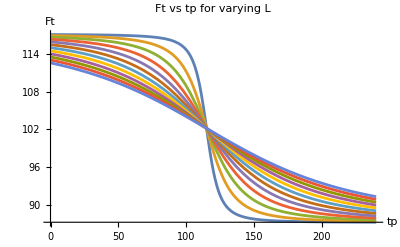

```mathematica
Plot[Evaluate@Table[FLtrue[L,tp],{L,500,6000,500}],{tp,0,240},PlotRange->All,AxesLabel->{"tp","Ft"},PlotLabel->"Ft vs tp for varying L"]
```

### 5. Calculate L from the slope of the Doppler at (t0p, f0).

### Plot the slope (here we assume that l is known):

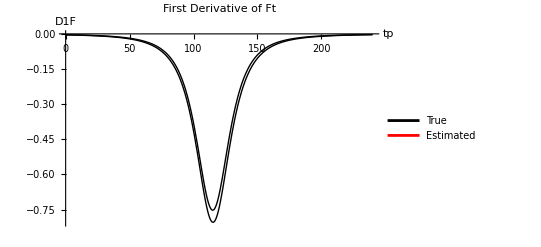

```mathematica
Plot[{
Style[D1F[v0,tp0,l,f0,c,tp],Black],
Style[D1F[v0X,tp0X,l,FtX,cX,tp],Red]},{tp,0,240},PlotLegends->{"True","Estimated"},PlotLabel->"First Derivative of Ft",AxesLabel->{"tp","D1F"},PlotRange->All]
```

### Measure the slope by choosing two points on the linear section, then solve for L. KEY POINT: tp is set equal to tp0, so we are looking at the peak slope at the center of the Doppler curve.

```mathematica
FullSimplify[D1F[v0z,tp0z,lz,f0z,cz,tp0z]]
```

(cz^3 f0z v0z^2)/((2 cz lz^2 v0z^2)/(√((lz^2 (cz-v0z) (cz+v0z))/cz^4))-cz^4 √((cz^2 lz^2)/(cz^2-v0z^2))-v0z^4 √((cz^2 lz^2)/(cz^2-v0z^2)))

### Cleaner expression, which factors out 1/L

```mathematica
vfactor[v0_,c_]:=v0^2/c(1-(v0/c)^2)^(-3/2)
```

```mathematica
Lfactor[v0_,f0_,c_]:=-f0 vfactor[v0,c]
```

```mathematica
D1Forigin[v0_,l_,f0_,c_]:=Lfactor[v0,f0,c]/l
```

### check that the “full simplify” expression reduces to the very clean version in D1Forigin:

```mathematica
D1Forigin[v0X,L,FtX,cX]
Simplify[D1F[v0X,tp0X,L,FtX,cX,tp0X]]
```

-804.278/L

-804.278/(√(L^2))

### solve for L:

```mathematica
xslope =-0.8;
Lfactor[v0X,FtX,cX]/xslope
```

1005.35

```mathematica
f0
```

100

```mathematica
N[vfactor[v0,c]]
```

7.52728

### a numerical solve will produce + and - values:

```mathematica
Solve[D1F[v0X,tp0X,L,FtX,cX,tp0X]==xslope,L]
```

{{L→-1005.35},{L→1005.35}}

### The number is slightly different if you use the measured slope and the true spectrum:

```mathematica
Solve[D1F[v0,tp0,L,f0,c,tp0]==xslope,L]
Lfactor[v0,f0,c]/xslope
```

{{L→-940.91},{L→940.91}}

940.91

## Derivatives w.r.t. time

### Note: the roots of the third derivative give time values at the inflection points.

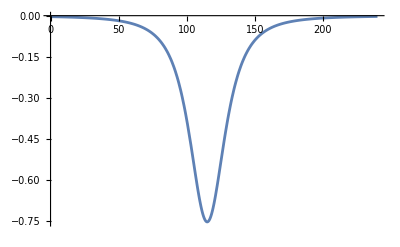

```mathematica
Plot[D1F[v0,tp0,l,f0,c,tp],{tp,0,240},PlotRange->All]
```

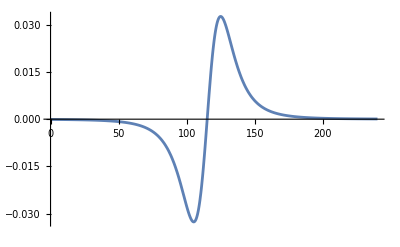

```mathematica
Plot[D2f[v0,tp0,l,f0,c,tp],{tp,0,240},PlotRange->All]
```

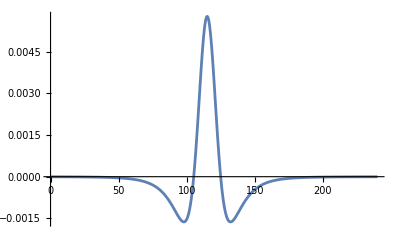

```mathematica
Plot[D3f[v0,tp0,l,f0,c,tp],{tp,0,240},PlotRange->All]
```

## Partial derivatives for v0, tp0, l, f0, c

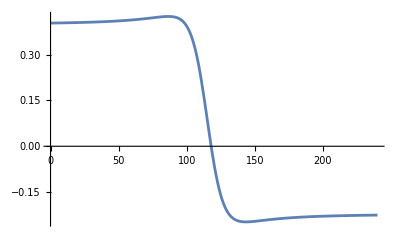

```mathematica
Plot[partialv[v0,tp0,l,f0,c,tp],{tp,0,240}]
```

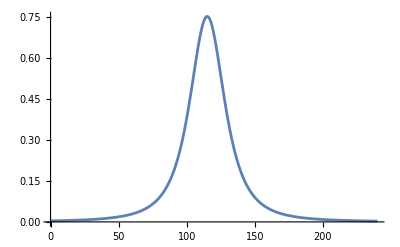

```mathematica
Plot[partialtp[v0,tp0,l,f0,c,tp],{tp,0,240}]
```

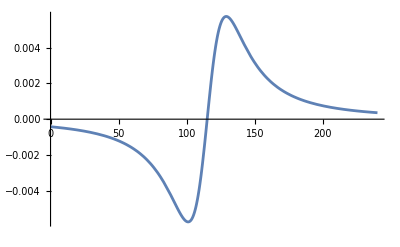

```mathematica
Plot[partiall[v0,tp0,l,f0,c,tp],{tp,0,240}]
```

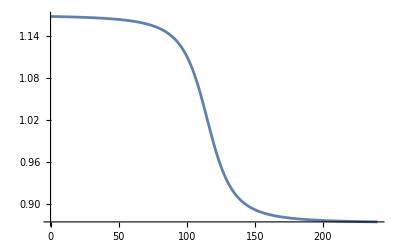

```mathematica
Plot[partialf[v0,tp0,l,f0,c,tp],{tp,0,240}]
```

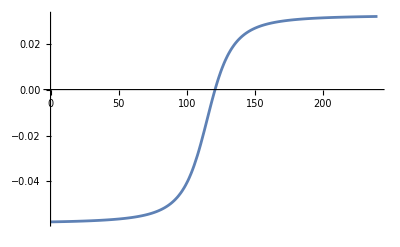

```mathematica
Plot[partialc[v0,tp0,l,f0,c,tp],{tp,0,240}]
```

## Test values (for checking Python)

```mathematica
tp = 100;
```

```mathematica
N[t[v0,tp0,l,c,tp]]
N[Ft[v0,tp0,l,f0,c,tp]]
N[G[v0,tp0,l,c,tp]]
N[partialv[v0,tp0,l,f0,c,tp]]
N[partialtp[v0,tp0,l,f0,c,tp]]
N[partiall[v0,tp0,l,f0,c,tp]]
N[partialf[v0,tp0,l,f0,c,tp]]
N[partialc[v0,tp0,l,f0,c,tp]]
```

-19.0237

111.169

3.61945

0.393254

0.380922

-0.00571383

1.11169

-0.0406672